```mathematica
sig[x_]:=1/(1+E^(-x))
```

```mathematica
nn[x_,θ_,f_:Tanh]:=Module[{w11,w12,w13,w14,w21,w22,w23},
{w11,w12,w13,w14,w21,w22,w23} = θ;
Return[f[w21*f[w11*x+w12]+w22*f[w13*x+w14]+w23]];
 Return[f[w21*f[w11*f[x]+w12]+w22*f[w13*f[x]+w14]+w23]];
Return[w21*f[w11*x+w12]+w22*f[w13*x+w14]+w23];
]
```

```mathematica
gradient[x_,weights_,fn_:Tanh]:=Module[{w11,w12,w13,w14,w21,w22,w23,w,d},
w={w11,w12,w13,w14,w21,w22,w23};
d=D[nn[x,w,fn],{w}]/.MapThread[#1->#2&,{w,weights}];
Return[d]
]
```

```mathematica
D[-1/2(y-nn[x,{w11,w12,w13,w14,w21,w22,w23},f])^2,{{w11,w12,w13,w14,w21,w22,w23}}]//TableForm
```

w21 x (y-f[w23+w21 f[w12+w11 x]+w22 f[w14+w13 x]]) f'[w12+w11 x] f'[w23+w21 f[w12+w11 x]+w22 f[w14+w13 x]]
w21 (y-f[w23+w21 f[w12+w11 x]+w22 f[w14+w13 x]]) f'[w12+w11 x] f'[w23+w21 f[w12+w11 x]+w22 f[w14+w13 x]]
w22 x (y-f[w23+w21 f[w12+w11 x]+w22 f[w14+w13 x]]) f'[w14+w13 x] f'[w23+w21 f[w12+w11 x]+w22 f[w14+w13 x]]
w22 (y-f[w23+w21 f[w12+w11 x]+w22 f[w14+w13 x]]) f'[w14+w13 x] f'[w23+w21 f[w12+w11 x]+w22 f[w14+w13 x]]
f[w12+w11 x] (y-f[w23+w21 f[w12+w11 x]+w22 f[w14+w13 x]]) f'[w23+w21 f[w12+w11 x]+w22 f[w14+w13 x]]
f[w14+w13 x] (y-f[w23+w21 f[w12+w11 x]+w22 f[w14+w13 x]]) f'[w23+w21 f[w12+w11 x]+w22 f[w14+w13 x]]
(y-f[w23+w21 f[w12+w11 x]+w22 f[w14+w13 x]]) f'[w23+w21 f[w12+w11 x]+w22 f[w14+w13 x]]

```mathematica
(*
Implement a simple backpropagation algorithm and print out the
weights along the way. Use this to really understand what is 
going on. And then use it as a way to generate data to test your
software with. Eg, you can generate the entire sequience of weights,
 outputs, and errors for 10, 100, or even 1000 iterations of 
backpropagation and use that to verify your python program.
*)
```

```mathematica
train[data_,init_,lr_:.1,epochs_:100]:=Module[{θ,errors,adjust,batches},
θ=init;
Do[
errors = Map[d↦{d[[1]],d[[2]]-nn[d[[1]],θ]},data];
adjust =Table[θ +=gradient[e[[1]],θ]*e[[2]]*lr,{e,errors}];
(*,{e,RandomSample[errors,10]}]*)
(* θ += Mean@adjust *)
,{epochs}]
Return[θ];
]
```

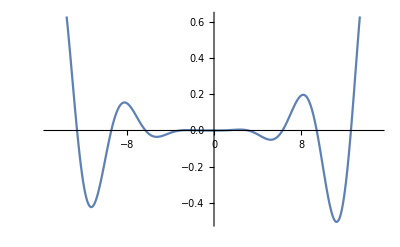

```mathematica
Plot[(x+x^2+x^3)*Sin[x]/3000,{x,-15,15}]
```

```mathematica
data={{2,.9},{1,.3},{-1,.4},{-2,.1}};
data2=Table[{x,(x+x^2+x^3)*Sin[x]/4000},{x,-15,15,.5}];
θ = {.4,-.2,.6,.1,.4,-.2,.6};
```

{0.44548,-8.1177,0.211708,3.06551,1.40588,-0.306272,1.52515}

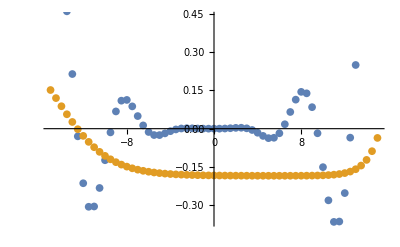

```mathematica
nθ = train[data2, θ,.01,10000]
nnData =Map[in ↦{in, nn[in,nθ]},data2[[All,1]]];
ListPlot[{data2,nnData}]
```

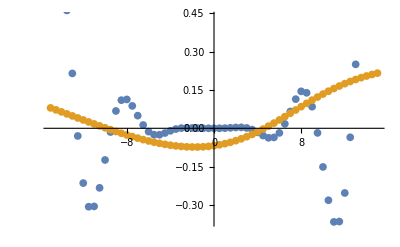

```mathematica
ListPlot[Flatten[θs,1]ᵀ]
```

-Graphics-

```mathematica
NonlinearModelFit[data,a+b*x+c*x^2+d*x^3,{a,b,c,d},x]
```

FittedModel[0.3-0.133333 x+0.05 x^2+0.0833333 x^3]

```mathematica
(* Create a general neural network structure generator. That can be
used to graph the network, produce partial derivative table, and other metadata. *)
NODES = "nodes";
ACTIVATION = "activation";
BIASED = "biased";
nnConfig={
<|NODES->2, ACTIVATION->Subscript[f, in], BIASED->True|>,
<|NODES->2, ACTIVATION->Subscript[f, hid], BIASED->True|>,
<|NODES->1, ACTIVATION->Subscript[f, out], BIASED->False|>
};
```

```mathematica
nnStruct=NetworkStructure[nnConfig]
```

{{f_in[x_1],f_in[x_2],1},{f_hid[x_1],f_hid[x_2],1},{f_out[x_1]}}

```mathematica
FullyConnected[nnStruct]
```

{f_out[w_(2,3)+w_(2,1) f_hid[w_(1,3)+w_(1,1) f_in[x_1]+w_(1,2) f_in[x_2]]+w_(2,2) f_hid[w_(1,6)+w_(1,4) f_in[x_1]+w_(1,5) f_in[x_2]]]}

```mathematica
NetworkStructure[config_]:=Module[{nodes,activation,biased},
nodes=c↦c[[NODES]]+If[c[[BIASED]],1,0];
Return[
Table[
If[n>c[[NODES]],1,c[[ACTIVATION]][Subscript[x, n]]]
,{c,config},{n,nodes[c]}]
];
]
FullyConnected[nnStructure_/;Length[nnStructure]≤ 1,wIndex_:-1]:=Module[{},
Return[WeightedSum[nnStructure[[1]],1,wIndex]];
]

FullyConnected[nnStructure_/;Length[nnStructure]>1,wIndex_:-1]:=Module[{layerLength,node,recWIndex},
layerLength=Length[nnStructure[[-1]]];
Return[
WeightedSum[
Table[
node=nnStructure[[-1,i]];
recWIndex=(i-1)*layerLength;
node/.Subscript[x, i]-> FullyConnected[nnStructure[[1;;-2]],recWIndex]
,{i,1,layerLength}],
Length[nnStructure],wIndex]
];
]
WeightedSum[nnLayer_,nLayer_,wIndex_/;wIndex==-1]:=nnLayer

WeightedSum[nnLayer_,nLayer_,wIndex_]:=Module[
{sum,node,partIndex},
sum=0;
Do[
node=nnLayer[[i]];
partIndex = i+wIndex;
sum+=(Subscript[w, nLayer,partIndex])*node;
,{i,1,Length[nnLayer]}];
Return[sum];
]
```